```mathematica
Clear[ℳ0,ϕ1,ϕ2]
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}]
```

```mathematica
(*ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]);*)
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]);
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]);
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+(m^2-β^2)/(x-ω1)+(m^2-β^2)/(x-1)-(m^2-β^2)/(x-ω1+ω2)-(m^2-β^2)/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}];
```

```mathematica
If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=ω2>ω1
```

```mathematica
ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]+ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]
```

(1/ω2>ω1/ω2)+(1/ω2>(1-ω1+ω2)/ω2)+(ω2>ω1)+(ω2>1-ω1+ω2)+(ω1/(1-ω1+ω2)>1/(1-ω1+ω2))+(ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2))+((1-ω1+ω2)/ω1>1/ω1)+((1-ω1+ω2)/ω1>ω2/ω1)

```mathematica
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]
```

If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]

```mathematica
Block[{ϕ3,ϕ4,ϕ2,ϕ1,M3,M4,M2,M1},ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]]
```

NIntegrate::inumr: The integrand ((1+1/ω2-ω1/ω2) ω2^2 ϕ1[x] ϕ2[(y ω2)/ω1] ϕ3[(x (1+1/ω2-ω1/ω2) ω2)/(ω1 (1-ω2/ω1+((1+Power[«2»]+Times[«3»]) ω2)/ω1))] ϕ4[y])/(ω1^2 (((-1+y) ω2)/ω1+((1-x) (1+1/ω2-ω1/ω2) ω2)/ω1)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand (1+1/ω2-ω1/ω2) ϕ1[x] ϕ2[ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x (1+1/ω2-ω1/ω2) ω2)/ω1] ϕ3[(x (1+1/ω2-ω1/ω2) ω2)/(ω1 (1-ω2/ω1+((1+Power[«2»]+Times[«3»]) ω2)/ω1))] ϕ4[(ω1 (ω2/ω1-((1+1/ω2-ω1 Power[«2»]) ω2)/ω1+(x (1+1/ω2-ω1 Power[«2»]) ω2)/ω1))/ω2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-4 (-2000000 NIntegrate[1/((ω1 ω2)/ω1)((1+1/ω2-ω1/ω2) ω2) ϕ3[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ4[(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)] ϕ2[((ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1) ω2)/((ω2 ω1)/ω1)] ϕ1[x],{x,0,1}]+NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ3[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ4[y] ϕ2[(y ω2)/ω1] ϕ1[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,0,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)-λ}]+NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ3[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ4[y] ϕ2[(y ω2)/ω1] ϕ1[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)+λ,1}])

```mathematica
Module[{ϕ3,ϕ4,ϕ2,ϕ1,M3,M4,M2,M1},1/((ω1 ω2)/ω1)((1+1/ω2-ω1/ω2) ω2) ϕ3[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ4[(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)] ϕ2[((ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1) ω2)/((ω2 ω1)/ω1)] ϕ1[x]//Simplify]
```

((1-ω1+ω2) ϕ1$242191[x] ϕ2$242191[(-1+ω1+x (1-ω1+ω2))/ω1] ϕ3$242191[x (1-ω1+ω2)] ϕ4$242191[(-1+ω1+x (1-ω1+ω2))/ω2])/ω2

```mathematica
(#+ℛ@#)&@ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]
```

ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]

```mathematica
ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])
```

ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]

```mathematica
ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]
```

ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]

```mathematica
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=1>ω1
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=ω2>ω1
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=(ω2>ω1)&&(ω1>1)
```

```mathematica
{ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma],ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc],ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]}
```

{1>1/ω1,1>ω1,1>ω1/ω2,1>ω2/ω1}

```mathematica
Assuming[ω1>0&&ω2>0&&1-ω1+ω2>0,Simplify@#&/@%]
```

{ω1>1,ω1<1,ω2>ω1,ω1>ω2}

```mathematica
{ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc],ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]}
```

{ω2>ω1,1/ω2>ω1/ω2,ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2)}

```mathematica
Assuming[ω1>0&&ω2>0&&1-ω1+ω2>0,Simplify@#&/@%]
```

{ω2>ω1,ω1<1,ω1>1,ω1>ω2}

```mathematica
{ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma],ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc],ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb],ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]}
```

{(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1,ω2>ω1&&ω1>1,1/ω2>ω1/ω2&&ω1/ω2>1,ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2)&&1/((1+1/ω2-ω1/ω2) ω2)>1,((1+1/ω2-ω1/ω2) ω2)/ω1>ω2/ω1&&ω2/ω1>1,ω2>(1+1/ω2-ω1/ω2) ω2&&(1+1/ω2-ω1/ω2) ω2>1,ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2)&&ω2/(1-ω1+ω2)>1,1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1}

```mathematica
Assuming[ω1>0&&ω2>0&&1-ω1+ω2>0,Simplify@#&/@%]
```

{ω2>ω1&&ω1<1,ω2>ω1&&ω1>1,ω1<1&&ω1>ω2,ω1>1&&ω1>ω2,ω1<1&&ω2>ω1,ω1>1&&ω2>ω1,ω1>ω2&&ω1>1,ω1>ω2&&ω1<1}

```mathematica
Reduce[{#,ω1>0&&ω2>0&&1-ω1+ω2>0},ω1]&/@{ω2>ω1&&ω1<1,ω2>ω1&&ω1>1,ω1<1&&ω1>ω2,ω1>1&&ω1>ω2,ω1<1&&ω2>ω1,ω1>1&&ω2>ω1,ω1>ω2&&ω1>1,ω1>ω2&&ω1<1}
```

{(0<ω2≤1&&0<ω1<ω2)||(ω2>1&&0<ω1<1),ω2>1&&1<ω1<ω2,0<ω2<1&&ω2<ω1<1,(0<ω2≤1&&1<ω1<1+ω2)||(ω2>1&&ω2<ω1<1+ω2),(0<ω2<1&&0<ω1<ω2)||(ω2≥1&&0<ω1<1),ω2>1&&1<ω1<ω2,(0<ω2<1&&1<ω1<1+ω2)||(ω2≥1&&ω2<ω1<1+ω2),0<ω2<1&&ω2<ω1<1}

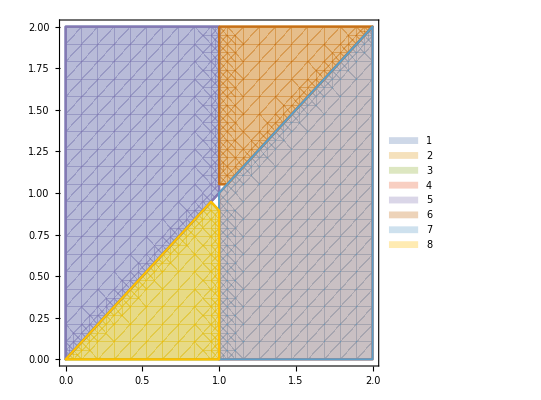

```mathematica
RegionPlot[%,{ω1,0,2},{ω2,0,2},PlotLegends->Automatic]
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Limit[-M1^2+M2^2+s- √(M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))//Simplify,s->∞]
```

2 M2^2

```mathematica
√s-(s+M1^2-M2^2)/(2 √s)-√(((s+M1^2-M2^2)/(2 √s))^2-M1^2)/.s->(M1+M2)^2//Simplify
```

(M2 (M1+M2))/(√((M1+M2)^2))

```mathematica
Manipulate[If[(M3+M4<M1+M2),ω1S[(M1+M2)^2][M1,M2,M3,M4],],{M1,0.001,10000},{M2,0.001,10000},{M3,0.001,10000},{M4,0.001,10000}]
```

```mathematica
Manipulate[If[(M3+M4<M1+M2),ω2S[(M1+M2)^2][M1,M2,M3,M4],],{M1,0.001,10000},{M2,0.001,10000},{M3,0.001,10000},{M4,0.001,10000}]
```

```mathematica
Manipulate[If[(M3+M4<M1+M2),ω1S[(M1+M2)^2][M1,M2,M3,M4]-ω2S[(M1+M2)^2][M1,M2,M3,M4],],{M1,0.001,10000},{M2,0.001,10000},{M3,0.001,10000},{M4,0.001,10000}]
```

```mathematica
1-(ω1S[(M1+M2)^2][M1,M2,M3,M4]-ω2S[(M1+M2)^2][M1,M2,M3,M4])//Simplify
```

(2 M1 (M1+M2))/(M1^2+2 M1 M2+M2^2+M3^2-M4^2+√((M1+M2)^2) √((M3^4+((M1+M2)^2-M4^2)^2-2 M3^2 ((M1+M2)^2+M4^2))/(M1+M2)^2))